# Vector Calculus

by Manuel Diaz, NTU, 2013.06.08
using Mathematica 9.0

```mathematica
Quit[]
```

## Basic Operations with vectors

### Dot product

```mathematica
{1,2,3}.{4,5,6}
```

32

```mathematica
Dot[{1,2,3}.{4,5,6}]
```

32

### Cross product

```mathematica
{1,2,3}×{4,5,6}
```

{-3,6,-3}

```mathematica
Cross[{1,2,3},{4,5,6}]
```

{-3,6,-3}

### Vector Plot

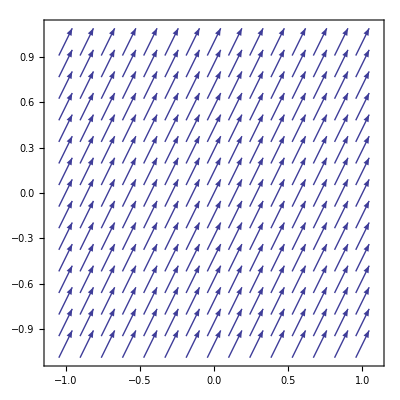

```mathematica
vector = {1,2};
VectorPlot[vector,{x,-1,1},{y,-1,1}]
```

again but with less arrows...

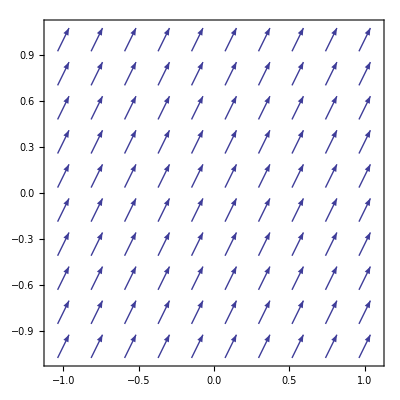

```mathematica
VectorPlot[vector,{x,-1,1},{y,-1,1},VectorPoints->{10,10},VectorScale->Small]
```

enough of a constant vector, choose:

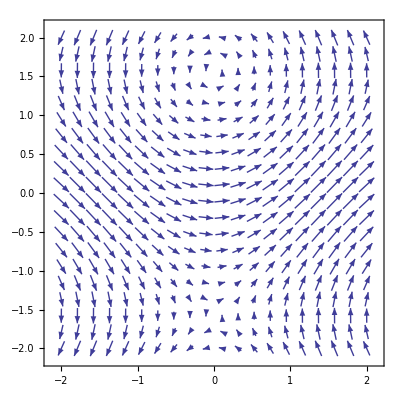

```mathematica
vectorfun[x_,y_] := {Cos[y],Sin[x]}
VectorPlot[vectorfun[x,y],{x,-2,2},{y,-2,2},VectorPoints->{20,20},VectorScale->0.05]
```

Let’s do it in 3D!

```mathematica
vectorfun3d[x_,y_,z_]:= {Sin[x],Cos[z],Sin[y]}
```

```mathematica
VectorPlot3D[vectorfun3d[x,y,z],{x,-Pi,Pi},{y,-Pi,Pi},{z,-Pi,Pi},VectorPoints->{10,10,10},VectorScale-> 0.06]
```

-Graphics3D-

Replot with axis label,

```mathematica
VectorPlot3D[vectorfun3d[x,y,z],{x,-Pi,Pi},{y,-Pi,Pi},{z,-Pi,Pi},VectorPoints->{10,10,10},VectorScale-> 0.06,AxesLabel->{X-axis,Y-axis,Z-axis}]
```

-Graphics3D-

### Contour Plots

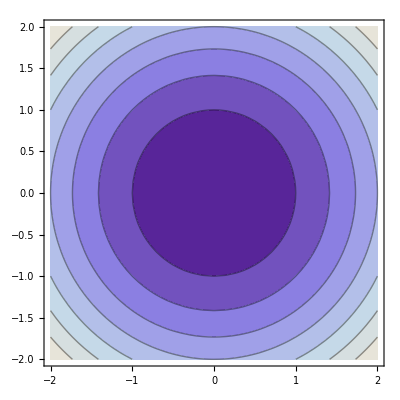

```mathematica
ContourPlot[x^2+y^2,{x,-2,2},{y,-2,2}]
```

how about an specif contour level?

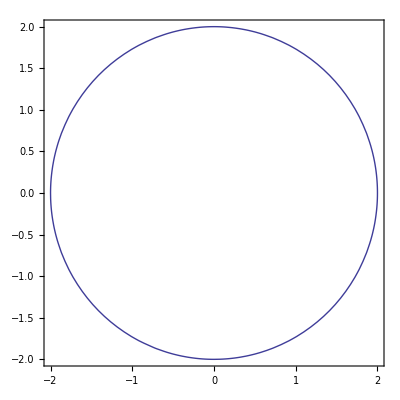

```mathematica
ContourPlot[x^2+y^2 == 4,{x,-2,2},{y,-2,2}]
```

Let’s do the same now with 3D vector field,

```mathematica
ContourPlot3D[x^2+y^2+z^2,{x,-2,2},{y,-2,2},{z,-2,2},AxesLabel->{X-axis,Y-axis,Z-axis}]
```

-Graphics3D-

again, given an specific field region

```mathematica
ContourPlot3D[x^2+y^2+z^2 ==4,{x,-2,2},{y,-2,2},{z,-2,2},AxesLabel->{X-axis,Y-axis,Z-axis}]
```

-Graphics3D-

### ParametricPlots & ParametricPlot3D

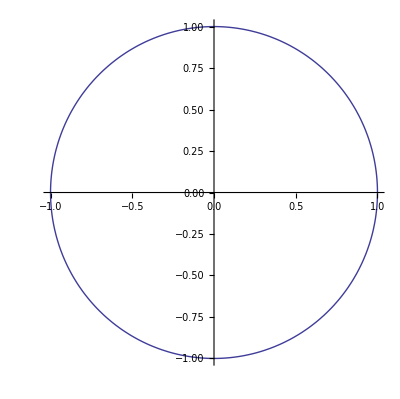

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,-π,π}]
```

Ok, let’s try to be more creative this time

```mathematica
parametricVector[a_,b_,c_,d_,j_,k_,t_]:= {Cos[a t]-(Cos[b t])^j,Sin[c t]-(Sin[d t])^k}
```

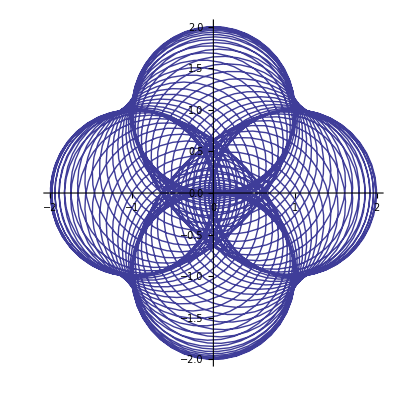

```mathematica
ParametricPlot[parametricVector[80,1,80,1,3,3,t],{t,0,2π}]
```

More examples we computed and posted in http://en.wikipedia.org/wiki/Parametric_equation

And now, ladies and gentlmens...  we are doint it in 3D!

```mathematica
ParametricPlot3D[{u-v,u+v,u*v},{u,-2,2},{v,-2,2},AxesLabel-> {X,Y,Z}]
```

-Graphics3D-

## Vector Calculus

To perform the following tricks we would need the VectorAnalysis package that is included in the common version of Mathematica 9.0,

```mathematica
Quit[];
```

```mathematica
Needs["VectorAnalysis`"]
```

Once is loaded in memory, the first task for us is to define the Coordiante system we are going to use:

### Set Coordinate system

```mathematica
SetCoordinates[Cartesian]
```

Cartesian(Xx,Yy,Zz)

```mathematica
SetCoordinates[Cylindrical]
```

Cylindrical(Rr,Ttheta,Zz)

```mathematica
SetCoordinates[Spherical]
```

Spherical(Rr,Ttheta,Pphi)

### Gradient

NOTE:  Gradient function  ≠ Grad function!

Remember that the input of a gradient is a vectorial function

```mathematica
f[a_,b_,c_]:=a b c
```

```mathematica
Grad[f[Xx,Yy,Zz],Cartesian]
```

{Yy Zz,Xx Zz,Xx Yy}

```mathematica
Grad[Xx*Yy*Zz,Cartesian]
```

{Yy Zz,Xx Zz,Xx Yy}

```mathematica
Grad[Rr*Ttheta*Zz,Cylindrical]
```

{Ttheta Zz,Zz,Rr Ttheta}

```mathematica
Grad[Rr*Ttheta*Pphi,Spherical]
```

{Pphi Ttheta,Pphi,Ttheta csc(Ttheta)}

Like Grad command, Diverge uses the same abreviation as in a calculus manual.

Do not forget that the input of the Diverge command is a vector of a scalar

```mathematica
f[a_,b_,c_]:={Exp[-a],Exp[-b],Exp[-c]}
```

```mathematica
Div[f[Xx,Yy,Zz],Cartesian]
```

-ⅇ^-Xx-ⅇ^-Yy-ⅇ^-Zz

```mathematica
Div[f[Rr,Ttheta,Zz],Cylindrical]
```

(-Rr ⅇ^-Zz-ⅇ^-Rr Rr+ⅇ^-Rr-ⅇ^-Ttheta)/Rr

```mathematica
Div[f[Rr,Ttheta,Pphi],Spherical]
```

1/Rr^2 csc(Ttheta) (-ⅇ^-Pphi Rr-ⅇ^-Rr Rr^2 sin(Ttheta)+2 ⅇ^-Rr Rr sin(Ttheta)-Rr ⅇ^-Ttheta sin(Ttheta)+Rr ⅇ^-Ttheta cos(Ttheta))

### Curl

The most tedious to compute by hand,

```mathematica
Curl[f[Xx,Yy,Zz],Cartesian]
```

{0,0,0}

```mathematica
Curl[f[Rr,Ttheta,Zz],Cylindrical]
```

{0,0,ⅇ^-Ttheta/Rr}

```mathematica
Curl[f[Rr,Ttheta,Pphi],Spherical]
```

{(ⅇ^-Pphi cot(Ttheta))/Rr,-ⅇ^-Pphi/Rr,ⅇ^-Ttheta/Rr}

Remember, the coordinate system you are working in matters a lot. If the latter two results look nasty 
and unfriendly, it’s because the original function didn’t have cylindrical or spherical symmetry

### Laplacian

Laplacian = Div . Grad ( f(x) )

```mathematica
Laplacian[g[x,y,z],{x,y,z},"Cartesian"]
```

Laplacian(g(x,y,z),{x,y,z},Cartesian)

```mathematica
Laplacian[f[Xx,Yy,Zz],Cartesian]
```

{ⅇ^-Xx,ⅇ^-Yy,ⅇ^-Zz}

```mathematica
Laplacian[f[Rr,Ttheta,Zz],Cylindrical]
```

{-(-Rr ⅇ^-Zz-ⅇ^-Rr Rr+ⅇ^-Rr-ⅇ^-Ttheta)/Rr^2+ⅇ^-Ttheta/Rr^2+(ⅇ^-Rr Rr-2 ⅇ^-Rr-ⅇ^-Zz)/Rr,0,ⅇ^-Zz}

```mathematica
Laplacian[Sin[Rr^2],{Rr,Ttheta},"Polar"]
```

Laplacian(sin(Rr^2),{Rr,Ttheta},Polar)

### Line Integrals

```mathematica
r[t_]:= {Cos[t],Sin[t],3t}
```

```mathematica
r'[t]
```

{-sin(t),cos(t),3}

```mathematica
∫_0^(2π) Dot[{3t,Cos[t],Sin[t]},r'[t]]ⅆt
```

7 π

```mathematica
∫_0^(2π) Dot[{Cos[t],Sin[t],3t},r'[t]]ⅆt
```

18 π^2

```mathematica
∫_0^(2π) Dot[r[t],r'[t]]ⅆt
```

18 π^2

Observation: my Ti-200 can compute the line integrals in the same manner

### Construction of Normal Vector

A surface integral operates very much like a line integral. The hardest part is finding a normal vector. 
First, the surface must be parameterized. A normal vector is found by taking partial derivatives and then 
calculating a cross product

```mathematica
r2[u_,v_]:={u,u^2,v}
```

```mathematica
n1= D[r2[u,v], u]
```

{1,2 u,0}

```mathematica
n2 =D[r2[u,v], v]
```

{0,0,1}

```mathematica
normalVector= Cross[n1,n2]
```

{2 u,-1,0}

### Surface Integrals

We are now ready to calculate a surface integral. The process will look much like a line integral. Instead 
of calculating all of the individual pieces by hand, I am going to plug everything into an integral. The 
machine itself is capable of doing all of the intermediary steps: partial derivatives, dot products, and 
cross products. This is something that can also be put into a TI-200.

```mathematica
∫_0^3 ∫_0^2 Dot[{3 v^2,6,6u v},Cross[D[r2[u,v], u],D[r2[u,v], v]]]ⅆuⅆv
```

72

or, using the later definition:

```mathematica
∫_0^3 ∫_0^2 Dot[{3 v^2,6,6u v},normalVector]ⅆuⅆv
```

72